```mathematica
SetDirectory[NotebookDirectory[]];
```

# Plotting the Differential Spectrum

#### Produce the spectra in a form dN/dz(z) to allow Tracy to set limits. Place the delta function weight at z=-1 so it can be easily extracted

## Define common factors

```mathematica
mW=80.385;(*GeV*)
αW=(1/137.035999139)/0.2223;
```

## Get Sommerfeld factors - s_00 and s_(0±) and hence F0 and F1

#### Load these in from Tracy’s files Take the real parts of the factors to remove tiny residual imaginary contributions

```mathematica
data=Get["./Sommerfeld_v=1e-3.dat"];
mvals=Table[data[[10i+1,1]],{i,0,23}];
Dimensions[mvals]
Log10[mvals]
mvals
F0vals=Table[Re[4/3 data[[10i+1,2]]*Conjugate[data[[10i+1,2]]]+2data[[10i+1,3]]*Conjugate[data[[10i+1,3]]]+(2 √2)/3(data[[10i+1,2]]*Conjugate[data[[10i+1,3]]]+data[[10i+1,3]]*Conjugate[data[[10i+1,2]]])],{i,0,23}]
F1vals=Table[Re[-4/3 data[[10i+1,2]]*Conjugate[data[[10i+1,2]]]+2data[[10i+1,3]]*Conjugate[data[[10i+1,3]]]-(2 √2)/3(data[[10i+1,2]]*Conjugate[data[[10i+1,3]]]+data[[10i+1,3]]*Conjugate[data[[10i+1,2]]])],{i,0,23}]
```

{24}

{2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3}

{100.,125.893,158.489,199.526,251.189,316.228,398.107,501.187,630.957,794.328,1000.,1258.93,1584.89,1995.26,2511.89,3162.28,3981.07,5011.87,6309.57,7943.28,10000.,12589.3,15848.9,19952.6}

{1.45468,1.49075,1.53926,1.6056,1.6982,1.83081,2.02698,2.32962,2.82338,3.69432,5.41759,9.51544,23.185,131.44,1273.46,66.5749,29.7271,25.9419,41.9624,226.686,586.478,83.5213,102.493,2010.38}

{-1.44147,-1.46972,-1.50568,-1.5517,-1.61108,-1.6886,-1.79147,-1.93132,-2.12825,-2.42051,-2.89093,-3.75669,-5.81042,-15.4081,-13.7723,3.82142,2.51757,2.01856,2.13972,4.73,0.00648447,-0.627295,-0.588687,-3.59121}

## Define differential spectrum

#### Define the δ-fn and continuum parts separately

```mathematica
DspecDelta[mDM_,F0_,F1_]=1/2 Exp[(-4αW)/π(Log[(2mDM)/mW])^2](F0+F1);
DspecCont[z_,mDM_,F0_,F1_]=1/2 Exp[(-4αW)/π(Log[(2mDM)/mW])^2](F0* HeavisideTheta[1-mW^2/(4 mDM^2)-z]*( (2αW)/π Log[(4 mDM^2(1-z))/mW^2] Exp[αW/π(Log[(4 mDM^2(1-z))/mW^2])^2]/(1-z))+F1*(((2αW)/π Log[(4 mDM^2(1-z))/mW^2]HeavisideTheta[1-mW^2/(4 mDM^2)-z]-(6αW)/π Log[(2mDM(1-z))/mW] HeavisideTheta[1-mW/(2mDM)-z])*(1/(1-z)Exp[-(3αW)/π(Log[(2mDM(1-z))/mW])^2 HeavisideTheta[1-mW/(2mDM)-z]+αW/π(Log[(4 mDM^2(1-z))/mW^2])^2 HeavisideTheta[1-mW^2/(4 mDM^2)-z]])));
```

#### Check ratio for Tracy

```mathematica
mvals[[14]]
DspecDelta[mvals[[14]],F0vals[[14]],F1vals[[14]]]
NIntegrate[DspecCont[z,mvals[[14]],F0vals[[14]],F1vals[[14]]],{z,0,1}]
DspecDelta[mvals[[14]],F0vals[[14]],F1vals[[14]]]/NIntegrate[DspecCont[z,mvals[[14]],F0vals[[14]],F1vals[[14]]],{z,0,1}]
```

1995.26

30.6741

30.8395

0.994637

```mathematica
mvals[[11]]
DspecDelta[mvals[[11]],F0vals[[11]],F1vals[[11]]]
NIntegrate[DspecCont[z,mvals[[11]],F0vals[[11]],F1vals[[11]]],{z,0,1}]
DspecDelta[mvals[[11]],F0vals[[11]],F1vals[[11]]]/NIntegrate[DspecCont[z,mvals[[11]],F0vals[[11]],F1vals[[11]]],{z,0,1}]
```

1000.

0.820359

0.844395

0.971535

```mathematica
mvals[[16]]
DspecDelta[mvals[[16]],F0vals[[16]],F1vals[[16]]]
NIntegrate[DspecCont[z,mvals[[16]],F0vals[[16]],F1vals[[16]]],{z,0,1}]
DspecDelta[mvals[[16]],F0vals[[16]],F1vals[[16]]]/NIntegrate[DspecCont[z,mvals[[16]],F0vals[[16]],F1vals[[16]]],{z,0,1}]
```

3162.28

15.8712

19.3794

0.818975

## Plot cumulative spectra as a sanity check

```mathematica
DspecDelta[mvals[[1]],F0vals[[1]],F1vals[[1]]]
```

0.00638129

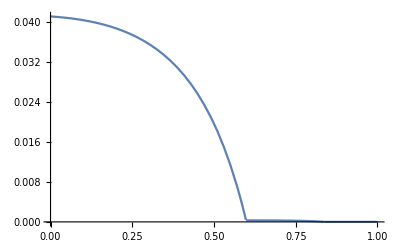

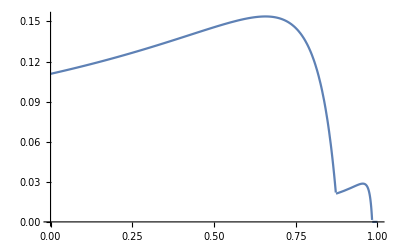

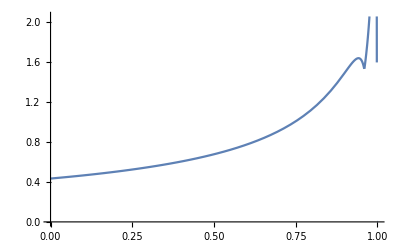

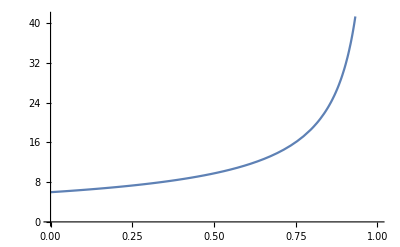

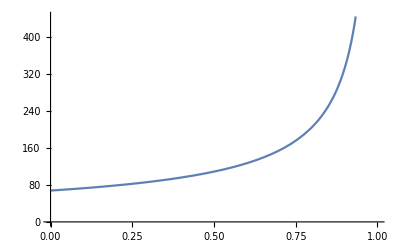

```mathematica
Plot[DspecCont[z,mvals[[1]],F0vals[[1]],F1vals[[1]]],{z,0,1}]
Plot[DspecCont[z,mvals[[6]],F0vals[[6]],F1vals[[6]]],{z,0,1}]
Plot[DspecCont[z,mvals[[11]],F0vals[[11]],F1vals[[11]]],{z,0,1}]
Plot[DspecCont[z,mvals[[16]],F0vals[[16]],F1vals[[16]]],{z,0,1}]
Plot[DspecCont[z,mvals[[21]],F0vals[[21]],F1vals[[21]]],{z,0,1}]
```

## Save values into a table

```mathematica
Output=Table[Join[{mvals[[i]],DspecDelta[mvals[[i]],F0vals[[i]],F1vals[[i]]]}, Table[DspecCont[1-10^(-0.01z),mvals[[i]],F0vals[[i]],F1vals[[i]]],{z,0,300}]],{i,1,Dimensions[mvals][[1]]}];
```

```mathematica
Table[1-10^(-0.01z),{z,0,300}];
```

## Plot values again as sanity check

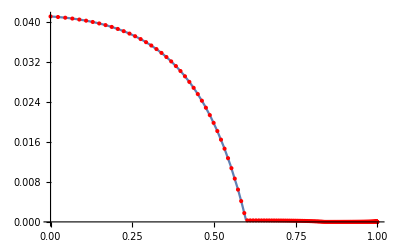

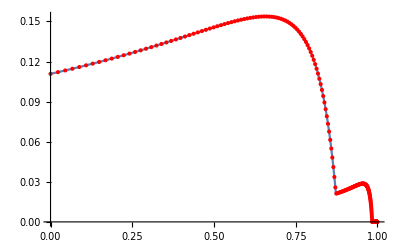

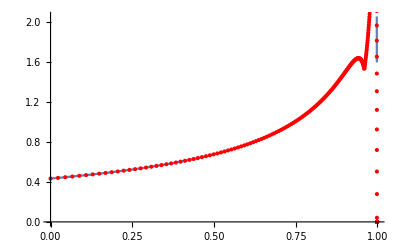

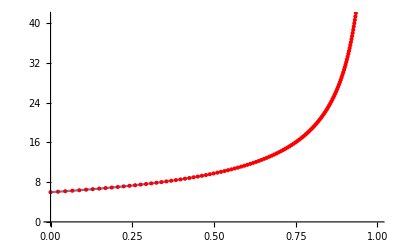

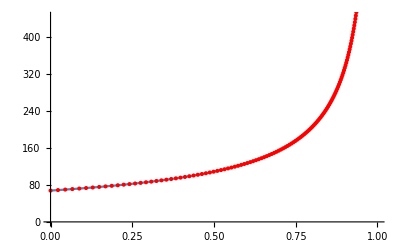

```mathematica
Show[Plot[DspecCont[z,mvals[[1]],F0vals[[1]],F1vals[[1]]],{z,0,1}],ListPlot[Table[{1-10^(-0.01i),Output[[1]][[i+3]]},{i,0,300}],PlotStyle->Red]]
Show[Plot[DspecCont[z,mvals[[6]],F0vals[[6]],F1vals[[6]]],{z,0,1}],ListPlot[Table[{1-10^(-0.01i),Output[[6]][[i+3]]},{i,0,300}],PlotStyle->Red]]
Show[Plot[DspecCont[z,mvals[[11]],F0vals[[11]],F1vals[[11]]],{z,0,1}],ListPlot[Table[{1-10^(-0.01i),Output[[11]][[i+3]]},{i,0,300}],PlotStyle->Red]]
Show[Plot[DspecCont[z,mvals[[16]],F0vals[[16]],F1vals[[16]]],{z,0,1}],ListPlot[Table[{1-10^(-0.01i),Output[[16]][[i+3]]},{i,0,300}],PlotStyle->Red]]
Show[Plot[DspecCont[z,mvals[[21]],F0vals[[21]],F1vals[[21]]],{z,0,1}],ListPlot[Table[{1-10^(-0.01i),Output[[21]][[i+3]]},{i,0,300}],PlotStyle->Red]]
```

## Output

```mathematica
Export["./Output/BinnedSpectra.dat",Output]
```

./Output/BinnedSpectra.dat